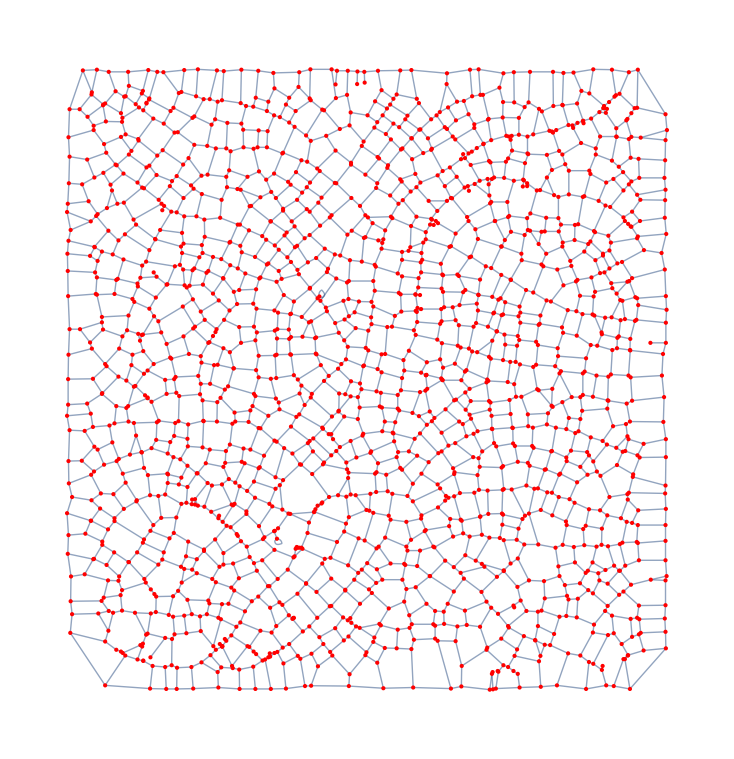

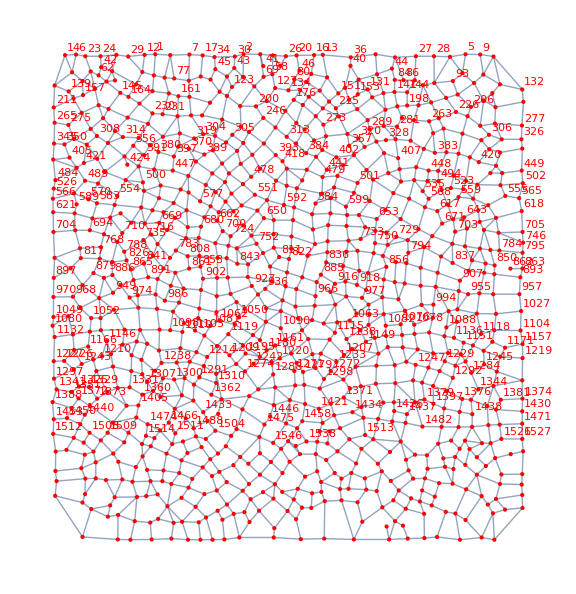

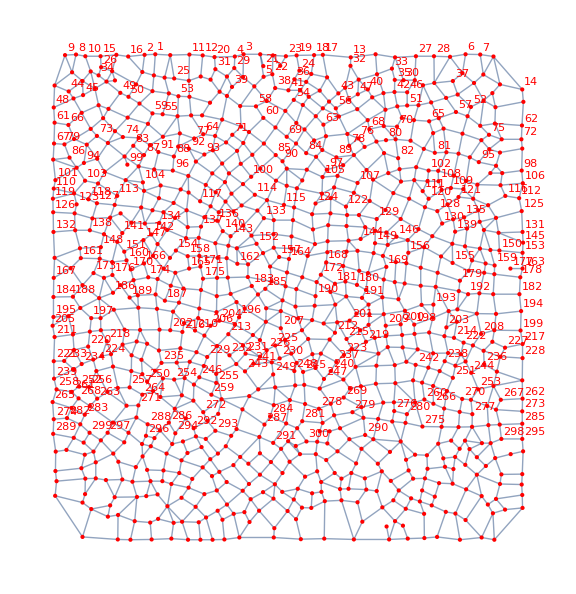

```mathematica
image=-Graphics-;
p1=Binarize[ImagePad[image,ImageDimensions[image][[1]]*0.05]];
p2=Thinning[DeleteSmallComponents[ColorNegate[DeleteSmallComponents[p1,300]],300]];
p2=Pruning[p2];
p2=Thinning[p2];
img=p2;
g=MorphologicalGraph[img,PlotRangePadding->2,VertexStyle->Red]

vcoords=AssociationThread[VertexList[g],GraphEmbedding[g]];
bottomthreshold=30.;
vlists=Select[Length@#>1&]@Gather[VertexList[g],Norm[vcoords[#]-vcoords[#2]]≤bottomthreshold&];
g2=SetProperty[Fold[VertexContract,g,vlists],{VertexLabels->"Name",ImageSize->Large,VertexCoordinates->{v_:>vcoords[v]}}]
IndexGraph[g2]
```